```mathematica
(*a= AdjacencyMatrix[GridGraph[{2,5}]]+IdentityMatrix[10]; *)
(*a = Table[1,{i,1,10},{j,1,10}];*)

(* Specialization Optimized*)
 (*a = AdjacencyMatrix[CirculantGraph[10,{1,3,5,7,9}]]+IdentityMatrix[10]; *)

(* Neighbor Graph*)
(*a = AdjacencyMatrix[CirculantGraph[10,{1}]]+IdentityMatrix[10];*)

(*Large Group*)
(*a = AdjacencyMatrix[CirculantGraph[10,{1}]]+IdentityMatrix[10];*)

(*Random Graph *)
(*a = AdjacencyMatrix@RandomGraph[{10,10}]+IdentityMatrix[10];*)

(* Full Graph *)
(*a = AdjacencyMatrix[CompleteGraph[10]] + IdentityMatrix[10];*)

(*Snowflake graph with 10 individuals*)
(*Snowflake10 = {1<->2,1<->3,1<->10,1<->9,2<->4,2<->6,3<->5,3<->7,6<->8};
a = AdjacencyMatrix@Graph[Snowflake10]+IdentityMatrix[10];*)

(*Filament Graph*)
a= AdjacencyMatrix[GridGraph[{1,10}]]+IdentityMatrix[10];

one = Table[1,{i,1,10}];
q = a* (1/Outer[Times,one.a,one]);
q//MatrixForm
```

(1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 1/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 1/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 1/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2)

```mathematica
Clear[h]
h[α_,β_]:= -α β q + (α β -1)IdentityMatrix[10];
```

```mathematica
e = Eigenvalues[h[α,β]];
eqns = Table[e[[i]]==0 , {i,1,10}];
soltns = α/.Table[Solve[eqns[[i]],{α}],{i,2,10}];
```

```mathematica
minSoltn = soltns[[First@Ordering[Flatten@(soltns/.{β->1}//N)]]][[1]];
```

```mathematica
Min[Flatten@(Abs@(minSoltn/.β->1//N))]
```

0.763287

```mathematica
Clear[a,one,q,h,e,eqns,soltns,minSoltn];
minSnowflakeSoltn[gens0_]:=Module[{gens=gens0},a = AdjacencyMatrix@CompleteKaryTree[gens,1] + IdentityMatrix[gens];one = Table[1,{i,1,gens}];
q = a* (1/Outer[Times,one.a,one]);
h = -α q + (α -1)IdentityMatrix[gens];
e = Eigenvalues[h];
eqns = Table[e[[i]]==0 , {i,1,gens}];
soltns =α/.Table[Solve[eqns[[i]],{α}],{i,2,gens}];
sol = {gens,First@Sort[Flatten@(Re/@soltns)//N]}
]
```

```mathematica
Clear[a,one,q,h,e,eqns,soltns,minSoltn];
minNeighborSoltn[n0_]:=Module[{n=n0},a = AdjacencyMatrix[CirculantGraph[n,{1}]]+IdentityMatrix[n];one = Table[1,{i,1,n}];
q = a* (1/Outer[Times,one.a,one]);
h = -α q + (α -1)IdentityMatrix[n];
e = Eigenvalues[h];
eqns = Table[e[[i]]==0 , {i,1,n}];
soltns =α/.Table[Solve[eqns[[i]],{α}],{i,2,n}];
sol = {n,First@Sort[Flatten@(Re/@soltns)//N]}
]
```

{16,0.721432}

```mathematica
minSnowflakeDat = Table[minSnowflakeSoltn[gen],{gen,2,120}]
```

{{2,1.},{3,0.857143},{4,0.813859},{5,0.793488},{6,0.781892},{7,0.774537},{8,0.76953},{9,0.765948},{10,0.763287},{11,0.76125},{12,0.759655},{13,0.75838},{14,0.757344},{15,0.756491},{16,0.755779},{17,0.755179},{18,0.754668},{19,0.75423},{20,0.75385},{21,0.75352},{22,0.753231},{23,0.752976},{24,0.75275},{25,0.752549},{26,0.75237},{27,0.752208},{28,0.752063},{29,0.751931},{30,0.751812},{31,0.751704},{32,0.751605},{33,0.751514},{34,0.751431},{35,0.751354},{36,0.751284},{37,0.751219},{38,0.751158},{39,0.751103},{40,0.751051},{41,0.751002},{42,0.750957},{43,0.750915},{44,0.750876},{45,0.750839},{46,0.750804},{47,0.750772},{48,0.750741},{49,0.750712},{50,0.750685},{51,0.750659},{52,0.750635},{53,0.750612},{54,0.750591},{55,0.75057},{56,0.75055},{57,0.750532},{58,0.750514},{59,0.750498},{60,0.750482},{61,0.750467},{62,0.750452},{63,0.750438},{64,0.750425},{65,0.750412},{66,0.7504},{67,0.750389},{68,0.750378},{69,0.750367},{70,0.750357},{71,0.750347},{72,0.750338},{73,0.750329},{74,0.750321},{75,0.750312},{76,0.750304},{77,0.750297},{78,0.750289},{79,0.750282},{80,0.750275},{81,0.750269},{82,0.750262},{83,0.750256},{84,0.75025},{85,0.750245},{86,0.750239},{87,0.750234},{88,0.750229},{89,0.750224},{90,0.750219},{91,0.750214},{92,0.750209},{93,0.750205},{94,0.750201},{95,0.750197},{96,0.750193},{97,0.750189},{98,0.750185},{99,0.750181},{100,0.750178},{101,0.750174},{102,0.750171},{103,0.750168},{104,0.750165},{105,0.750162},{106,0.750159},{107,0.750156},{108,0.750153},{109,0.75015},{110,0.750148},{111,0.750145},{112,0.750142},{113,0.75014},{114,0.750138},{115,0.750135},{116,0.750133},{117,0.750131},{118,0.750129},{119,0.750126},{120,0.750124}}

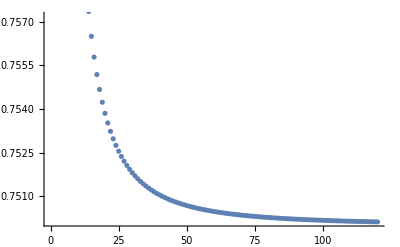

```mathematica
ListPlot[minSnowflakeDat]
```

```mathematica
data = Table[{i,minSnowflakeDat[[i]]},{i,1,Length@minSnowflakeDat}]
```

{{1,0.0156001},{2,0.},{3,0.0156001},{4,0.0624004},{5,0.109201},{6,0.171601},{7,0.826805},{8,1.10761},{9,1.51321},{10,1.77841},{11,2.05921},{12,2.43362},{13,2.91722},{14,3.63482},{15,4.27443},{16,5.27283},{17,6.44284},{18,7.65965},{19,9.36006},{20,11.3257},{21,13.5409},{22,16.3957},{23,19.7029}}

```mathematica
nlm = NonlinearModelFit[data, c x^power,{c,power},x]
```

FittedModel[0.000372112 x^3.45737]

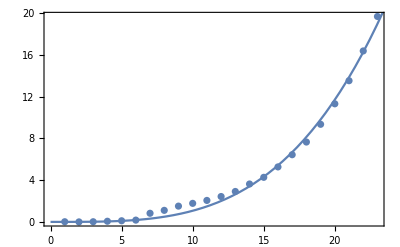

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,0,25}],Frame->True]
```

```mathematica
nlm[120]/60
```

95.725

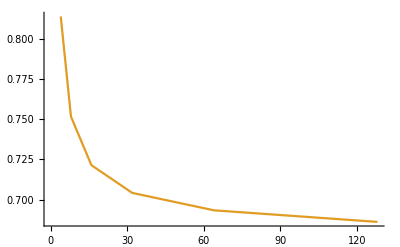

```mathematica
ListPlot[minSnowflakeDat,Joined->True]
```

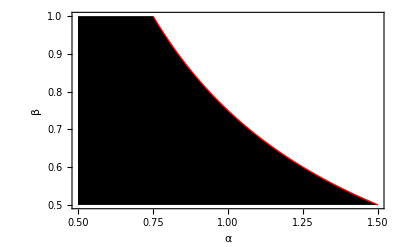

```mathematica
Plot[3/(4α),{α,.5,1.5}, PlotRange->{{0.5,1.5},{.5,1.0}},PlotStyle->{Thick,Red},Filling->{1->Bottom, 1->Top}, FillingStyle->{White,Black},Frame->{True,True,False,False},FrameLabel->{α,β},Axes->False]
```

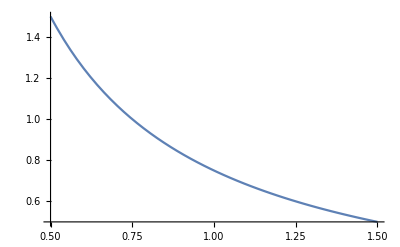

```mathematica
Plot[minSoltn,{α,.5,1.5}]
```

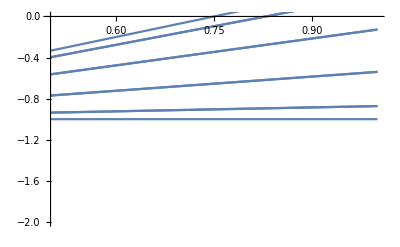

```mathematica
Show[Table[Plot[e[[i]]/.{α->1},{β,0.5,1}],{i,1,10}]]
```

```mathematica
h[α,β]//MatrixForm
```

(-1+(2 α β)/3 | 0 | 0 | 0 | -(α β)/3 | 0 | 0 | -(α β)/3 | 0 | 0
0 | -1+(2 α β)/3 | 0 | 0 | 0 | -(α β)/3 | 0 | 0 | -(α β)/3 | 0
0 | 0 | -1+(2 α β)/3 | 0 | 0 | 0 | 0 | -(α β)/3 | -(α β)/3 | 0
0 | 0 | 0 | -1+(2 α β)/3 | 0 | 0 | -(α β)/3 | 0 | 0 | -(α β)/3
-(α β)/3 | 0 | 0 | 0 | -1+(2 α β)/3 | 0 | 0 | 0 | -(α β)/3 | 0
0 | -(α β)/3 | 0 | 0 | 0 | -1+(2 α β)/3 | 0 | -(α β)/3 | 0 | 0
0 | 0 | 0 | -(α β)/2 | 0 | 0 | -1+(α β)/2 | 0 | 0 | 0
-(α β)/4 | 0 | -(α β)/4 | 0 | 0 | -(α β)/4 | 0 | -1+(3 α β)/4 | 0 | 0
0 | -(α β)/4 | -(α β)/4 | 0 | -(α β)/4 | 0 | 0 | 0 | -1+(3 α β)/4 | 0
0 | 0 | 0 | -(α β)/2 | 0 | 0 | 0 | 0 | 0 | -1+(α β)/2)

```mathematica
Clear[a,one,q,h,e,eqns,soltns,minSoltn];
minRandSoltn[α0_,β0_,nNodes0_,nEdges0_]:=Module[{α=α0, β=β0,nEdges=nEdges0,nNodes=nNodes0},a = AdjacencyMatrix@RandomGraph[{nNodes,nEdges}]+IdentityMatrix[nNodes];one = Table[1,{i,1,nNodes}];
q = a* (1/Outer[Times,one.a,one]);
h = -α β q + (α β -1)IdentityMatrix[nNodes];
e = Eigenvalues[h];
sol = 0.5+ 1/2 Sign[Max[e]]
]
```

```mathematica
minRandSoltn[1,1,10,45]
```

0.5

```mathematica
Binomial[20,2]
```

190

```mathematica
randRes = Table[Mean@Table[minRandSoltn[alph,bet,20],{i,1,100}],{bet,1,.5,-.02},{alph, .5,1.5,.02}];
```

```mathematica
Show[ArrayPlot[randRes,Frame->None,ColorFunction->GrayLevel],Frame->{True,True,False,False},FrameLabel->{α,β}]
```

-Graphics-

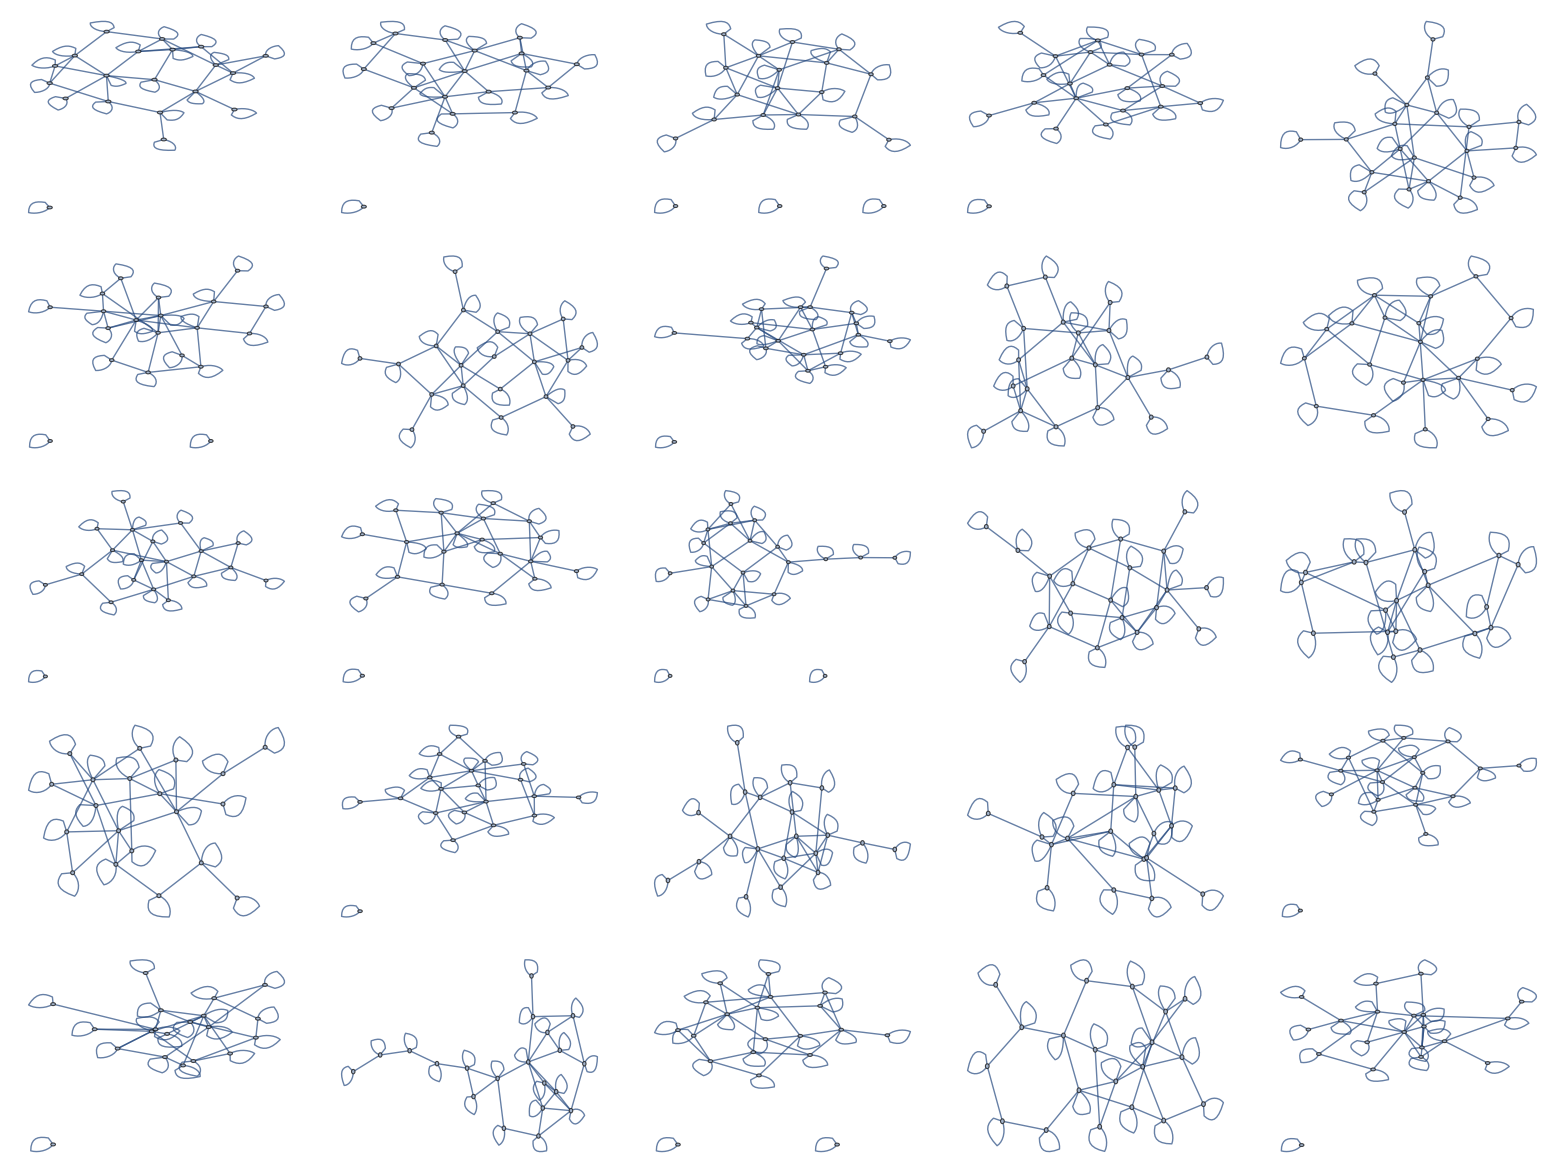
(-Graphics-)

(1/4 | 1/4 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | 0
1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0
1/4 | 0 | 0 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1/4 | 0 | 1/4 | 1/4 | 0 | 0 | 1/4 | 0 | 0
1/3 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 1/3 | 0
0 | 0 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | 0 | 1/3)

```mathematica
Table[Show[AdjacencyGraph[AdjacencyMatrix@RandomGraph[{20,30}]+IdentityMatrix[20],GraphLayout->{"SpringEmbedding"}],ImageSize->Small],{i,1,5},{j,1,5}]//MatrixForm
```

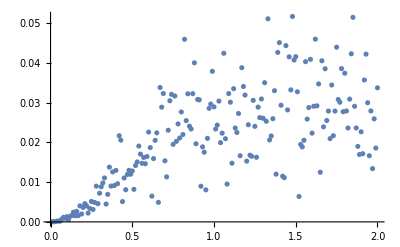

```mathematica
gradbW[v_,α_]:=(v^α).(q-IdentityMatrix[10]).(1-v)^α;
vs = Table[Table[.5+.2*RandomReal[],{i,1,10}],{j,.01,2,.01}];
alphs = Table[alph, {alph,.01,2,.01}];
ListPlot[Table[{alphs[[i]],gradbW[vs[[i]],alphs[[i]]]},{i,1,Length@alphs}]]
```

```mathematica
(v^2).(q-IdentityMatrix[10]).(1-v)^2
```

0.00022346

```mathematica
a = AdjacencyMatrix[CompleteGraph[6]]+IdentityMatrix[6]; 
one = Table[1,{i,1,6}];
q = a* (1/Outer[Times,one.a,one]);
q//MatrixForm//TeXForm
```

\left(
\begin{array}{cccccc}
 \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} \\
 \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} \\
 \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} \\
 \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} \\
 \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} \\
 \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} & \frac{1}{6} \\
\end{array}
\right)

```mathematica
g = AdjacencyGraph[AdjacencyMatrix[CompleteGraph[6]]+IdentityMatrix[6], GraphLayout->"CircularEmbedding"]
```

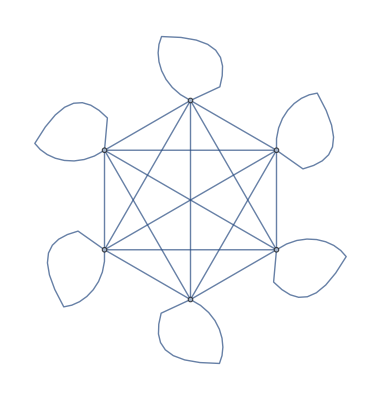

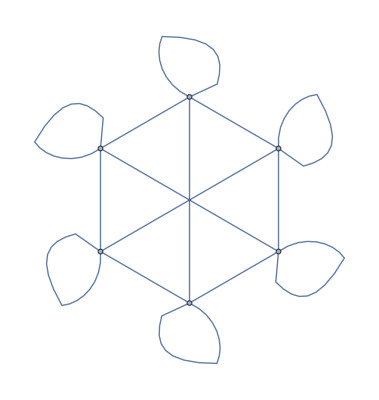

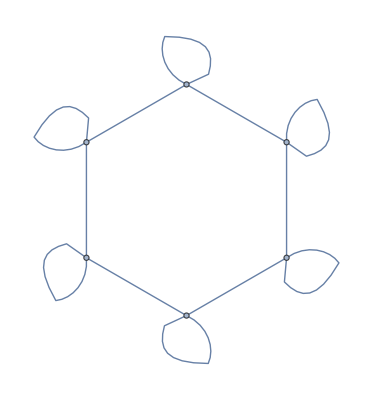

```mathematica
Norm[q-IdentityMatrix[6]]
```

1

```mathematica
dat = Table[{size,Timing[Table[Mean@Table[minRandSoltn[alph,1,size,n],{i,1,100}],{n,1,10},{alph, .5,1.0,.01}]][[1]]},{size,5,25}]
```

{{5,5.42883},{6,5.94364},{7,6.41164},{8,7.06685},{9,7.48805},{10,9.42246},{11,9.89046},{12,10.4989},{13,11.3569},{14,12.2305},{15,13.0261},{16,13.8685},{17,14.8201},{18,15.8497},{19,16.9885},{20,17.9869},{21,19.2037},{22,20.5297},{23,21.9025},{24,23.1661},{25,24.5702}}

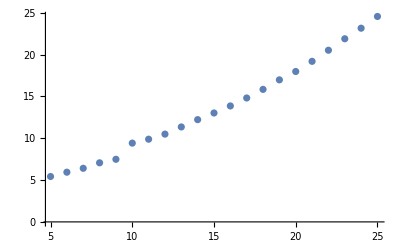

```mathematica
ListPlot[dat]
```

```mathematica
nlm = NonlinearModelFit[dat,c x^pow,{c,pow},x]
```

FittedModel[0.72776 x^1.07964]

```mathematica
nlm[100]
```

105.021

```mathematica
nedges = Table[i,{i,1,4950,10}];
randRes = Table[Mean@Table[minRandSoltn[alph,1,100,nedges[[n]]],{i,1,100}],{n,1,Length@nedges},{alph, .5,1.0,.01}]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5},493,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,19,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.9,1.}}
 |  |  |  |

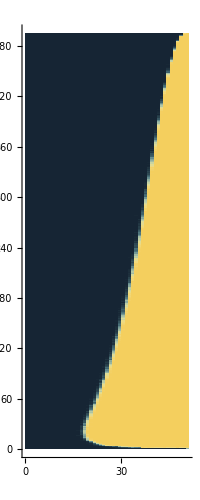

```mathematica
ArrayPlot[Reverse@randRes,ColorFunction->"StarryNightColors",Axes->True,FrameStyle->Directive[Black,Thickness[0.005]]]
```

```mathematica
Binomial[100,2]
```

```mathematica
Table[i,{i,1,4950,100}]
```

{1,101,201,301,401,501,601,701,801,901,1001,1101,1201,1301,1401,1501,1601,1701,1801,1901,2001,2101,2201,2301,2401,2501,2601,2701,2801,2901,3001,3101,3201,3301,3401,3501,3601,3701,3801,3901,4001,4101,4201,4301,4401,4501,4601,4701,4801,4901}

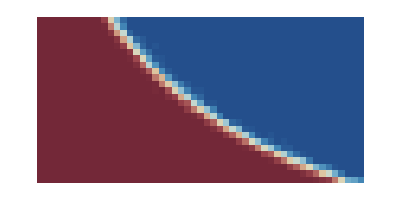

```mathematica
ArrayPlot[randRes,ColorFunction->"RedBlueTones"]
```

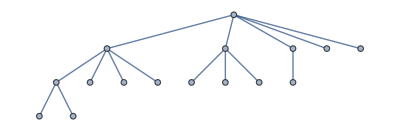

```mathematica
Graph@Flatten@Table[j<->(j+2^i),{j,1,6},{i,j-1,4}]
```

```mathematica
Flatten@{Table[{1<->i},{i,2,5}],Table[{2<->i},{i,6,8}]}
```

{1<->2,1<->3,1<->4,1<->5,2<->6,2<->7,2<->8}

```mathematica
flake[gen_]:=AdjacencyGraph@(AdjacencyMatrix@Graph@Flatten@Table[Table[{j<->i},{i,(j-1)*gen- Total@(Table[n,{n,1,j-1}])+2,j*gen - Total@(Table[n,{n,1,j}])+1}],{j,1,gen}]+IdentityMatrix[Total@Table[k,{k,1,gen-1}]+1])
```

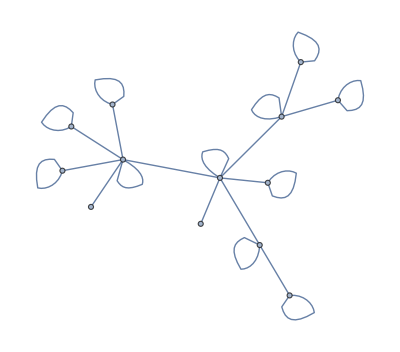

```mathematica
Graph@Flatten@{EdgeList@flake[5],{1<->99,2<->100}}
```

```mathematica
Flatten[%58]
```

{1<->1,1<->2,1<->3,1<->4,1<->5,2<->2,2<->6,2<->7,2<->8,3<->3,3<->9,3<->10,4<->4,4<->11,5<->5,6<->6,7<->7,8<->8,9<->9,10<->10,11<->11,1<->99,2<->100}

```mathematica
yeast[graph0_]:=Module[{graph=graph0},nodes = VertexList@graph; n = Length@nodes; newNodes = Table[i,{i,n+1,2n}]; newEdges = Table[nodes[[i]]<->newNodes[[i]],{i,1,n}]; newSelfLoops = Table[newNodes[[i]]<->newNodes[[i]],{i,1,n}];newGraph = Graph@Flatten@{EdgeList@graph, newEdges,newSelfLoops}]
```

```mathematica
g = Graph[{1<->1}];
```

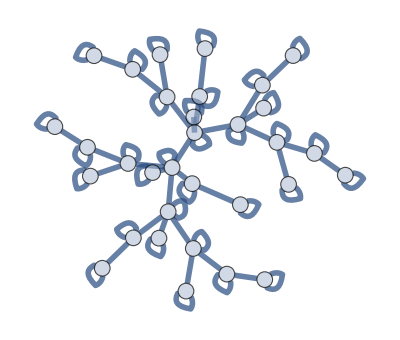

```mathematica
g = Graph[{1<->1}];
g = Nest[yeast,g,5];
Graph[EdgeList@g,VertexSize->1,GraphLayout->"SpringEmbedding",EdgeStyle->Thickness[.01],VertexStyle->Opacity[.5]]
```

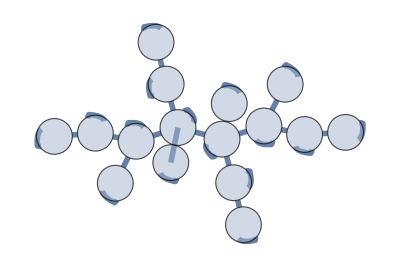

Set::write: Tag Inherited in Inherited[State] is Protected.

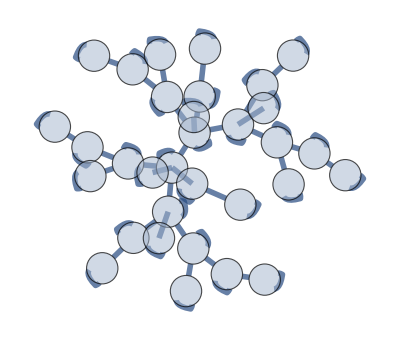

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
AdjacencyMatrix[%74]//MatrixForm
```

(1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

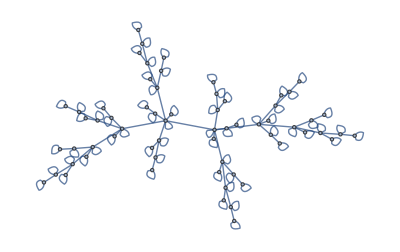
GraphLayout[-Graphics-,CircularEmbedding]

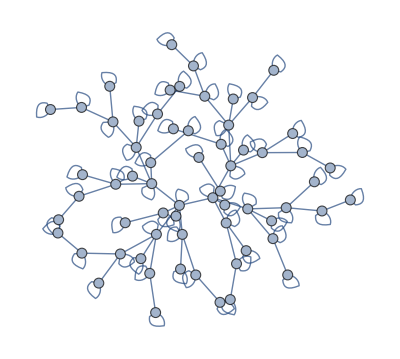

```mathematica
GraphLayout[g,"CircularEmbedding"]
```

```mathematica
AdjacencyMatrix@g//MatrixForm
```

(1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Export["un_dat.csv",minSnowflakeDat]
```

un_dat.csv

```mathematica
SystemOpen["un_dat.csv"]
```

```mathematica
SystemOpen["unaryDat.csv"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["snowflakeTreesDat.csv"]]]
```

```mathematica
SystemOpen["snowflakeTreesDat.csv"]
```

```mathematica
Snowflake10 = {1<->2,1<->3,1<->5,1<->9,2<->4,2<->6,2<->10,3<->7,4<->8}
```

{1<->2,1<->3,1<->5,1<->9,2<->4,2<->6,2<->10,3<->7,4<->8}

```mathematica
a = AdjacencyMatrix@Graph[Snowflake10]+IdentityMatrix[10]
```

{{1,1,1,1,1,0,0,0,0,0},{1,1,0,0,0,1,1,1,0,0},{1,0,1,0,0,0,0,0,1,0},{1,0,0,1,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,1},{0,1,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,1}}